#### ConceptualComputational

## Straight lines

### Formatting

```mathematica
DarkGreen:=Green//Darker//Darker
```

```mathematica
labelst[str_]:=Style[str,14,FontFamily->"Arial",Background->White]
```

```mathematica
myn[n_]:=labelst[If[Abs[n]<.0001,NumberForm[0.0,4],NumberForm[n,4]]]
```

```mathematica
myn[8.0^-5]
```

0.

```mathematica
Head[myn[8.9]]
```

Style

```mathematica
labelst[cu["a"]//TraditionalForm]
```

a^3-a

```mathematica
Remove[fsty]
```

```mathematica
fsty[f_,x_]:=Text[labelst[f[x]]//TraditionalForm]
```

```mathematica
fsty[cu,"a"]
```

cu(a)

### Point-slope form

```mathematica
ptsl[m_,p_,x_]:=m x+ p[[2]]-m p[[1]]
```

```mathematica
ptsl[m_,p_,x_]:=m (x-p[[1]])+ p[[2]]//Simplify
```

```mathematica
ptsl[3,{1,2},x]
```

-1+3 x

### Two-point form

```mathematica
tpl[p_,q_,x_]:=(p[[2]]-q[[2]])/(p[[1]]-q[[1]])(x-p[[1]])+p[[2]]//Simplify
```

```mathematica
tpl[{1,2},{0,-1},x]
```

-1+3 x

```mathematica
tpl[{0,-1},{1,2},x]
```

-1+3 x

```mathematica
tpl[{1,4},{5,2},x]
```

(9-x)/2

### Intersection of projections

Given two points, find intersection of horizontal line through one point and vertical line through the other

```mathematica
wh[{a1_,a2_},{b1_,b2_}]:={b1,a2}
```

```mathematica
wh[{.3,.5},{.8,.6}]
```

{0.8,0.5}

## Definitions

### Definitions

```mathematica
cu[x_]:=x^3-x;cud[x_]:=cu'[x]
```

```mathematica
labelst[str_]:=Style[str,14,FontFamily->"Arial",Background->White];
tline[a_,x_]:=ptsl[cud[a],{a,cu[a]},x];
(*offs:=.3;*)
u[x_,offs_]:={x+offs,ptsl[cud[x],{x,cu[x]},x+offs]};
v[x_,offs_]:={x-offs,ptsl[cud[x],{x,cu[x]},x-offs]};
corner[x_,offs_]:={v[x,offs][[1]],u[x,offs][[2]]};
secline[a_,b_,x_]:=If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
```

```mathematica
corner[.8,.3]
```

{0.5,-0.012}

```mathematica
corner[x,.3]
```

{-0.3+x,-0.3-1. x+0.9 x^2+x^3}

```mathematica
secline[.9,1.2,x]
```

-2.268+2.33 x

## Secants

```mathematica
tpl[{a,cu[a]},{b,cu[b]},x]
```

(-1+b^2) x+a^2 (-b+x)+a b (-b+x)

```mathematica
ptsl[cud[1],{1,cu[1]},x]
```

2 (-1+x)

```mathematica
Manipulate[
Show[
Plot[
{cu[x],
If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
},
{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{-2.2,2.2}},PlotStyle->{Blue,DarkGreen},
AspectRatio->4.4/3
],
Graphics[
{Black,
PointSize[.02],
Point[{a,cu[a]}],
Point[{b,cu[b]}]
}
]
],
{{a,-1},-1.5,1.5},{{b,.5},-1.5,1.5},
SaveDefinitions->True,Paneled->False
]
```

### Using secline

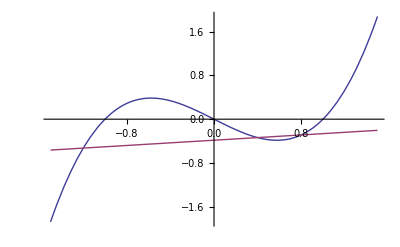

```mathematica
Plot[{cu[x],secline[.8,.4,x]},{x,-1.5,1.5}]
```

## Derivative' s value is slope of tangent line

### Calculations for input function, output slope

```mathematica
{.2,ptsl[cud[.2],{1,cu[.2]},.3]}
```

{0.2,0.424}

### Tangent line

```mathematica
Manipulate[
Row[{Show[
{
Plot[
{cu[x],tline[a,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->300
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],
DarkGreen,
Point[u[a,offs]],Point[v[a,offs]],Point[corner[a,offs]],
Line[{u[a,offs],corner[a,offs]}],Line[{v[a,offs],corner[a,offs]}],
Inset[labelst["w"],.5(u[a,offs]+corner[a,offs])],Inset[labelst["ht"],.5(v[a,offs]+corner[a,offs])]
}]
}
],
"    ",
Column[{"          ",
Grid[{{labelst["Input:"],labelst["x"],labelst["="],myn[a]}}],
Grid[{{labelst["Output:"],fsty[cu,"x"],labelst["="],myn[cu[a]]}}],
Grid[{{labelst["Width:"],labelst[2 offs]}}],
Grid[{{labelst["Height:"],myn[corner[a,offs][[2]]-v[a,offs][[2]]]}}],
Grid[{{labelst["Slope of tan line = height/width ="], myn[(corner[a,offs][[2]]-v[a,offs][[2]])/(2 offs)]}}],
Grid[{{labelst["Deriv.Output:"],fsty[cu',"x"],"=",myn[cu'[a]]}}],
}]}],
{{a,-.85,"x"},-1.25,1.25},{{offs,.35,"offset"},.01,.7},
SaveDefinitions->True,Paneled->False]
```

```mathematica
Manipulate[
Row[{Show[
{
Plot[
{cu[x],tline[a,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->300
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],
DarkGreen,
Point[u[a,offs]],Point[v[a,offs]],Point[corner[a,offs]],
Line[{u[a,offs],corner[a,offs]}],Line[{v[a,offs],corner[a,offs]}],
Inset[labelst["w"],.5(u[a,offs]+corner[a,offs])],Inset[labelst["ht"],.5(v[a,offs]+corner[a,offs])]
}]
}
],
"    ",
Column[{"          ",
Grid[{{labelst["Input:"],labelst["x"],labelst["="],myn[a]}}],
Grid[{{labelst["Output:"],fsty[cu,"x"],labelst["="],myn[cu[a]]}}],
Grid[{{labelst["Width:"],labelst[2 offs]}}],
Grid[{{labelst["Height:"],myn[corner[a,offs][[2]]-v[a,offs][[2]]]}}],
Grid[{{labelst["Slope of tan line = height/width ="], myn[(corner[a,offs][[2]]-v[a,offs][[2]])/(2 offs)]}}],
Grid[{{labelst["Deriv.Output:"],fsty[cu',"x"],"=",myn[cu'[a]]}}],
}]}],
{{a,-.85,"x"},-1.25,1.25},{{offs,.35,"offset"},.01,.7},
SaveDefinitions->True,Paneled->False]
```

### Notes

The width is always nonnegative.  The height is measured from the tangent line.

## Definitions for epsilon-delta meaning

```mathematica
dvdef[f_,x_,h_]:=(f[x+h]-f[x])/h
```

```mathematica
dvdef[cu,x,h]
```

(-h-x^3+(h+x)^3)/h

```mathematica
myn[dvdef[cu,.4,.2]]
```

-0.24

```mathematica
cu'[x]//TraditionalForm
```

3 x^2-1

### tests

```mathematica
labelst[cu["a"]//TraditionalForm]
```

a^3-a

```mathematica
Grid[{{fsty[cu,"a"],"=",myn[cu[3]]}}]
```

a^3-a | = | 24

```mathematica
Grid[{{fsty[dvdef["cu","a","h"]],"=",dvdef[cu,.8,.1]}}]
```

fsty[(-cu[a]+cu[a+h])/h] | = | 1.17

```mathematica
Module[{aa=.8,hh=.3},Line[{{aa,cu[aa]},{aa+hh,secline[aa,aa+hh,aa+hh]}}]]
```

Line[{{0.8,-0.288},{1.1,0.231}}]

#### test

```mathematica
Manipulate[
Graphics[
{PointSize[.02],Brown,
Line[{{a,cu[a]},{a+h,secline[a,a+h,a+h]}}]}
],
{{a,-.8},-1.25,1.25},{{h,.03},10^(-10),.05},
SaveDefinitions->True,Paneled->False]
```

```mathematica
Manipulate[
Show[{
Plot[
{cu[x],tline[a,x]},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->250
],
Graphics[
{PointSize[.02],Brown,Point[{a,cu[a]}],Point[{a+h,secline[a,a+h,a+h]}],
Line[{{a,cu[a]},{a+h,secline[a,a+h,a+h]}}]}
]
}],
{{a,-.8},-1.25,1.25},{{h,.03},10^(-10),1},
SaveDefinitions->True,Paneled->False]
```

```mathematica
Manipulate[
Row[{Show[
{
Plot[
{cu[x],tline[a,x]
},{x,-1.7,1.7},
PlotRange->{{-1.7,1.7},{-2,2}},
PlotStyle->{Blue,Red},AspectRatio->40/34,ImageSize->250
],
Graphics[
{PointSize[.02],
Point[{a,cu[a]}],Point[{a+h,secline[a,a+h,a+h]}],
DarkGreen,
Point[u[a]],Point[v[a]],Point[corner[a]],
Line[{u[a],corner[a]}],Line[{v[a],corner[a]}],
Inset[labelst["w"],.5(u[a]+corner[a])],Inset[labelst["ht"],.5(v[a]+corner[a])],
Brown,Point[{a,cu[a]}],Point[{a+h,secline[a,a+h,a+h]}],
Line[{{a,cu[a]},{a+h,secline[a,a+h,a+h]}}]
}]
}
],
"    ",
Column[{"          ",
labelst["a = "<>ToString[myn[a]]],
labelst["h = "<>ToString[myn[h]]],
Grid[{{fsty[cu,"a"],"=",myn[cu[a]]}}],
Grid[{{fsty[cu',"a"],"=",myn[cu'[a]]}}],
Grid[{{fsty[dvdef[cu,"a","h"]],"=",dvdef[cu,a,h]}}]}]
}],
{{a,-.8},-1.25,1.25},{{h,.03},10^(-10),1},
SaveDefinitions->True,Paneled->False]
```